```mathematica
Data[filename_]:= Module[{data},data=Transpose[Import[StringJoin["~/Desktop/projects/Thesis/datas/datas/",filename], "CSV"]];
Table[Thread[{data[[1]], data[[i]]}],{i, 2, Length[data]}]
]

Mech[filename_,pn_] :=Module[{data},
data=Data[filename];
plot = ListLinePlot[data,PlotLabels->{"y_1", "x_2","y_2", "x3", "y3"}, AxesLabel->{"x_1(mm)","mm"},PlotRange-> All];
Export[StringJoin["~/Desktop/projects/Thesis/datas/",pn, ".pdf"],plot];
plot
]
```

```mathematica
Sol[p1_,p2_, l_] :=Module[{data},
ed = Sqrt[(First@p2-First@p1)^2+(Last@p2-Last@p1)^2]-l;
be[x_] := Evaluate[ ed];
be
]
```

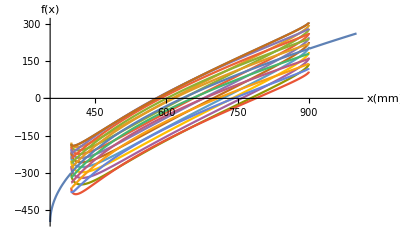

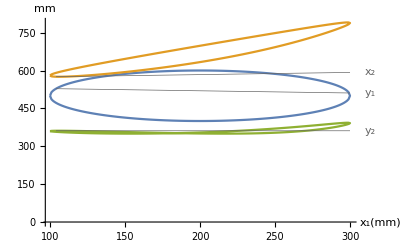

```mathematica
G[filename_, p2_, l_, d_, pn_]:= Module[{data},
data = Data[filename];
plot = Plot[Evaluate@Table[Sol[{data[[d,i, 1]], -data[[d,i, 2]]}, p2, l][x], {i, 1, Length[data[[1]]], 20}], {x, 0, 1000}, AxesLabel->{"x(mm)","f(x)"}, PlotRange->All];
Export[StringJoin["~/Desktop/projects/Thesis/datas/",pn,".pdf"],plot];
plot
]

G["mech1.csv", {x, ((1-(x-650)^2/250^2)*250^2)^(1/2)-600}, 500, 1, "mech1-graph-1"]
Mech["mech1.csv", "mech1-graph-2"]
```

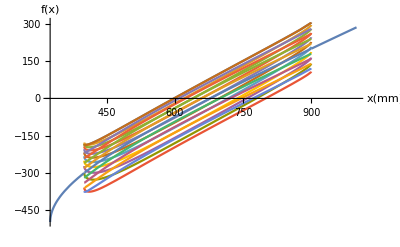

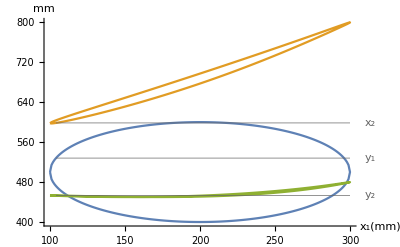

```mathematica
G["mech3.csv", {x, ((1-(x-650)^2/250^2)*150^2)^(1/2)-600}, 500, 1, "mech3-graph-1"]
Mech["mech3.csv", "mech3-graph-2"]
```

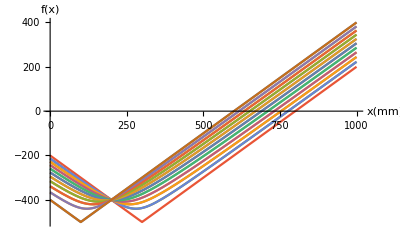

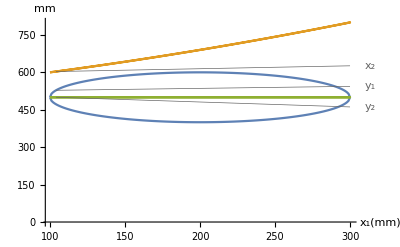

```mathematica
G["mech2.csv", {x, -500}, 500, 1, "mech2-graph-1"]
Mech["mech2.csv", "mech2-graph-2"]
```

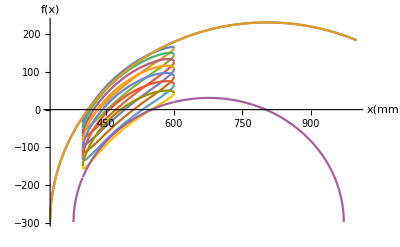

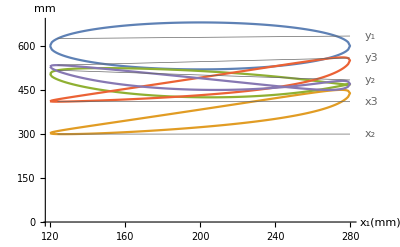

```mathematica
G["mech4-1.csv",  {x, ((1-(x-500)^2/100^2)*150^2)^(1/2)-600}, 300, 1,"mech4-graph-1"]
Mech["mech4-1.csv", "mech4-graph-2"]
```

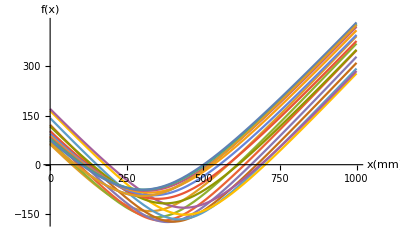

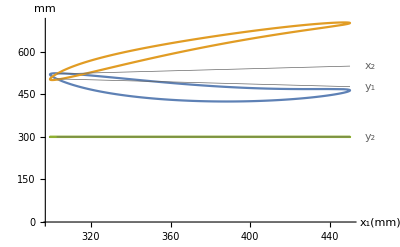

```mathematica
G["mech4.csv",  {x, -300}, 300, 1, "mech4-graph-3"]
Mech["mech4.csv", "mech4-graph-4"]
```